```mathematica
(*import=Import["/mnt/1T/last/mobile/flat/Pictures/Screenshots/time-all","Text"];*)
import=Import["/tmp/time","Text"];(*百度云和现在备份的*)
```

```mathematica
intItpr=Internal`StringToMInteger;
```

```mathematica
map={intItpr@#[[1]],intItpr@#[[2]]}&/@(StringSplit[#,"-"]&/@StringSplit[import,"\n"]);
```

```mathematica
parseDateTime[{d_,t_}]:=DateObject[
{
IntegerPart[d/10000],Mod[IntegerPart[d/100],100],Mod[d,100]}
~Join~{IntegerPart[t/10000],Mod[IntegerPart[t/100],100],Mod[t,100]
}
]
```

```mathematica
timeList=parseDateTime/@map;
```

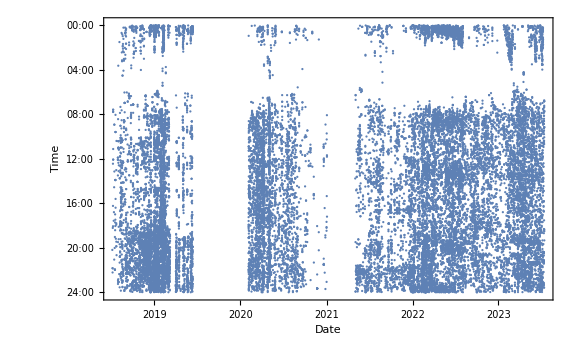

```mathematica
hours=DateValue[#,"HourExact"]&/@timeList;
data=MapThread[{#1,#2}&,{timeList,hours}];
ts=TimeSeries[data];
DateListPlot[ts,Joined->False,ScalingFunctions->"Reverse",FrameLabel->{"Date","Time"},ImageSize->Large,FrameTicks->{{Table[{x,StringRepeat["0",2-StringLength[ToString@x]]<>ToString@x<>":00"},{x,0,24,2}],None},{Automatic,None}},PlotRange->{Automatic,{-0.2,24.2}},
DateTicksFormat->{"Year","/","Month"}
]
```